## SSFEM for linear systems F. I. Giasemis

### Example

#### Implementation

```mathematica
Ψ[0]=1;
Ψ[1]=ξ;
Ψ[2]=ξ^2-1;
ξ[0]=1;
ξ[1]=ξ;
M=1;
p=2;
P=3;
K[0]=20000;
K[1]=2000;
q=280;
```

```mathematica
For[i=0,i≤1 ,i++,
For[j=0,j≤2,j++,
For[k=0,k≤2,k++,
c[i,j,k]=Integrate[ξ[i]Ψ[j]Ψ[k]Exp[-ξ^2/2]/Sqrt[2Pi],{ξ,-Infinity,Infinity}]
]
]
]
```

```mathematica
For[i=0,i≤2,i++,
F[i]=Integrate[Ψ[i]q Exp[-ξ^2/2]/Sqrt[2Pi],{ξ,-Infinity,Infinity}]
]
```

```mathematica
K[i_,j_]:=Sum[c[k,i,j] K[k],{k,0,1}]
```

```mathematica
Kbar={{K[0,0],K[0,1],K[0,2]},{K[1,0],K[1,1],K[1,2]},{K[2,0],K[2,1],K[2,2]}};
Fbar={F[0],F[1],F[2]};
```

```mathematica
{u[0],u[1],u[2]}=N[Inverse[Kbar].Fbar];
```

```mathematica
u=Sum[u[i] Ψ[i],{i,0,2}]
```

0.0141443-0.0014433 ξ+0.00014433 (-1+ξ^2)

```mathematica
list={};
For[M=0,M≤10000,M++,
ξ=RandomVariate[NormalDistribution[]];
AppendTo[list,Evaluate[u]];
]
```

#### Empirical pdf

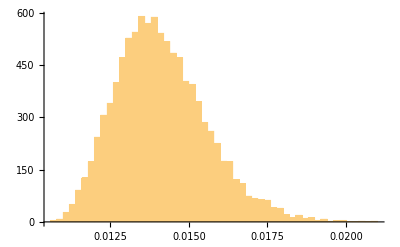

```mathematica
Histogram[list,40]
```